```mathematica
hbar=1.05457148×10(10)^-34; Delta = 9.2 10^12;Gam = 32.8 10^6/(2 Pi);λ = 852.1 10^-9; Inti = 2000;Ints = 3;alal = 2;k= 2 Pi/λ;
Clear[a,b,x,y,z,h]
Er = hbar^2 k^2/(2*(133 1.660 10^-27))
```

1.36943×10^-28

```mathematica
-2/3*hbar Gam^2 Inti / (Delta*8 Ints)
```

-1.73542×10^-31

```mathematica
Clear[a,b,x,y,z, hbar, Gam, Inti, Ints, Delta,k]
```

```mathematica
UD[x_,y_,z_,a_,b_]:=-2/3*hbar Gam^2 Inti / (Delta*8 Ints){Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y]}.{Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}
```

```mathematica
z=0;a = 0; b = Pi;
mi=FindMinimum[{UDsim[x,y,zf,a,b],{x,y,zf}∈ Sphere[{0,0,0},λ]} ,{x,y,zf}];
Manipulate[Show[{ListPlot3D[Table[UD[x,y,z,a,b]/Er,{x,-1 * λ,1 * λ, λ/10},{y,-1 * λ,1 * λ,λ/10}]],
Graphics[{PointSize[1],Point[{x/.mi[[2]], y/.mi[[2]],zf/.mi[[2]]}]}],

Graphics3D[Sphere[{x/.mi[[2]], y/.mi[[2]],zf/.mi[[2]]},1]]

}],{z,-1 * λ,1 * λ}]
```

Show::gcomb: Could not combine the graphics objects in ….

```mathematica
Graphics3D[Sphere[{x/.mi[[2]], y/.mi[[2]],zf/.mi[[2]]},1]]
```

-Graphics3D-

```mathematica
-2/3*hbar Gam^2 Inti / (Delta*8 Ints){Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y]}.{Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]} //FullSimplify
```

-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])

```mathematica
UDsim[x_,y_,z_,a_,b_]:=-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])
```

```mathematica
mi=FindMinimum[{UDsim[x,y,zf,0.1,0.2],{x,y,zf}∈ Sphere[{0,0,0},λ]} ,{x,y,zf}];
```

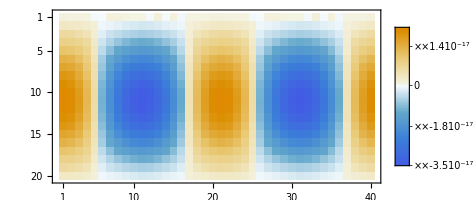

```mathematica
ho = 10^-10;  a= 0; b = 0;
mi=FindMinimum[{UDsim[x,y,zf,a,b],{x,y,zf}∈ Sphere[{0,0,0},λ]} ,{x,y,zf}];
x0=x/.mi[[2]]; y0=y/.mi[[2]]; z0=zf/.mi[[2]];
MatrixPlot[Table[cart = FromSphericalCoordinates[{1,θ,ϕ}]//N;

1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])

,{θ,0.0001 ,0.999 Pi, Pi/20},{ϕ,-Pi*0.999 , Pi, Pi/20}], PlotLegends -> True]
```

```mathematica
cart = FromSphericalCoordinates[{1,1,1}]//N
```

{0.454649,0.708073,0.540302}

```mathematica
x0+ ho cart[[1]]
```

(Cos[1] Sin[1])/10000000000

```mathematica
UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]
```

```mathematica
-1.8484820715395964*^-30
 2UDsim[x0,y0 ,z0,a,b]
```

-1.84848×10^-30

-3.69696×10^-30

```mathematica
UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b]
```

```mathematica
4.640678561856709*^-37 1/ho^2
```

4.64068×10^-17

```mathematica
1/ho^2(UDsim[x0+ ho cart[[1]],y0 +ho cart[[2]],z0 + ho cart[[3]],a,b]- 2UDsim[x0,y0 ,z0,a,b] + UDsim[x0-ho cart[[1]],y0 -ho cart[[2]],z0 - ho cart[[3]],a,b])
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of -9.99995×10^15 (3.47083×10^-31 (4+2. Cos[a]+2 Cos[0.+a+Times[«2»]]+2. Cos[b]+2 Sin[0.+a]+2. Sin[b])-1.73542×10^-31 («1»)-1.73542×10^-31 (4+Cos[a-b-0.00147475 Part[«2»]]+«5»+Sin[a-0.000737377 Part[«2»]+0.000737377 Part[«2»]])).

Hold[1/ho^2(UDsim[x0+ho cart⟦1⟧,y0+ho cart⟦2⟧,z0+ho cart⟦3⟧,a,b]-2 UDsim[x0,y0,z0,a,b]+UDsim[x0-ho cart⟦1⟧,y0-ho cart⟦2⟧,z0-ho cart⟦3⟧,a,b])]

```mathematica
-2/3*hbar Gam^2 Inti / (Delta*8 Ints){Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y]}.{Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}//FullSimplify
```

-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z])

```mathematica
LUDraw = Laplacian[-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z]),{x,y,z}] //FullSimplify
LUDrawx = D [D[-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z]),x],x] //FullSimplify
```

1/(3 Delta Ints)Gam^2 hbar Inti k^2 (Cos[a-b-2 k x]+Cos[a-b+2 k x]+Cos[a] Cos[k (x-y)]+Cos[b] Cos[k (x+y)]+Cos[k (x-z)] Sin[a]+Cos[k (x+z)] Sin[b])

1/(6 Delta Ints)Gam^2 hbar Inti k^2 (2 Cos[a-b-2 k x]+2 Cos[a-b+2 k x]+Cos[a] Cos[k (x-y)]+Cos[b] Cos[k (x+y)]+Cos[k (x-z)] Sin[a]+Cos[k (x+z)] Sin[b])

```mathematica
LUDrawy = D [D[-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z]),y],y] //FullSimplify
```

(Gam^2 hbar Inti k^2 (Cos[a] Cos[k (x-y)]+Cos[b] Cos[k (x+y)]))/(6 Delta Ints)

```mathematica
LUDrawz = D [D[-1/(12 Delta Ints)Gam^2 hbar Inti (4+Cos[a-b-2 k x]+Cos[a-b+2 k x]+2 Cos[a] Cos[k (x-y)]+2 Cos[b] Cos[k (x+y)]+2 Cos[k (x+z)] Sin[b]+Sin[a+k x-k z]+Sin[a-k x+k z]),z],z] //FullSimplify
```

(Gam^2 hbar Inti k^2 (Cos[k (x-z)] Sin[a]+Cos[k (x+z)] Sin[b]))/(6 Delta Ints)

```mathematica
z=0
Manipulate[ListPlot3D[Table[UD[x,y,z,0.3,0.1]/Er,{x,-1 * λ,1 * λ, λ/10},{y,-1 * λ,1 * λ,λ/10}]],{z,-1 * λ,1 * λ}]
```

0

```mathematica
a=0.1; b=0.3;z=12;Plot3D[1/Er  1/(3 Delta Ints)Gam^2 hbar Inti k^2 (Cos[a-b-2 k x]+Cos[a-b+2 k x]+Cos[a] Cos[k (x-y)]+Cos[b] Cos[k (x+y)]+Cos[k (x-z)] Sin[a]+Cos[k (x+z)] Sin[b]),{x,-2 * λ,2 * λ},{y,-2 * λ,2 * λ}]
```

-Graphics3D-

```mathematica
Clear[a,b,x,y,z,k]
```

```mathematica
ⅈ*Cross[{0, Sin[a]*Exp[ⅈ*k*x]+Sin[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*z],Cos[a]*Exp[ⅈ*k*x]+Cos[b]*Exp[-ⅈ*k*x]+Exp[ⅈ*k*y]},{0, Sin[a]*Exp[-ⅈ*k*x]+Sin[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*z],Cos[a]*Exp[-ⅈ*k*x]+Cos[b]*Exp[ⅈ*k*x]+Exp[-ⅈ*k*y]}]//FullSimplify
```

{2 (-Sin[a-b] Sin[2 k x]-Sin[a] Sin[k (x-y)]+Sin[b] Sin[k (x+y)]+Cos[a] Sin[k (x-z)]+Sin[k (y-z)]-Cos[b] Sin[k (x+z)]),0,0}

```mathematica
Ufm[x_,y_,z_,a_,b_]:= 1/3{2 (-Sin[a-b] Sin[2 k x]-Sin[a] Sin[k (x-y)]+Sin[b] Sin[k (x+y)]+Cos[a] Sin[k (x-z)]+Sin[k (y-z)]-Cos[b] Sin[k (x+z)]),0,0}
```

```mathematica
a=-Pi/6; b= Pi/6;z=0.5; k = 1;
Plot3D[Ufm[x,y,z,a,b][[1]],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
a=0; b= Pi/2;z=0.5; k = 1;
Plot3D[Sin[a]*Cos[k*x]+Sin[b]*Cos[-k*x]+Cos[k*z],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
a=0; b= Pi/2;z=0.5; k = 1;
Plot3D[Sin[a]*Cos[-k*x]+Sin[b]*Cos[k*x]+Cos[-k*z],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
Easier case
```

```mathematica
Clear[a,b,x,y,z,k]
```

```mathematica
epsilon = {Exp[i k x] + Cos[a]*Exp[-ⅈ k x], Sin[a] Exp[-ⅈ k x]}
```

{ⅇ^(-ⅈ x)+ⅇ^(i x),0}

```mathematica
{Exp[ⅈ k x] + Cos[a]*Exp[-ⅈ k x], Sin[a] Exp[-ⅈ k x]}.{Exp[-ⅈ k x] + Cos[a]*Exp[ⅈ k x], Sin[a] Exp[ⅈ k x]}//FullSimplify
```

2+2 Cos[a] Cos[2 k x]

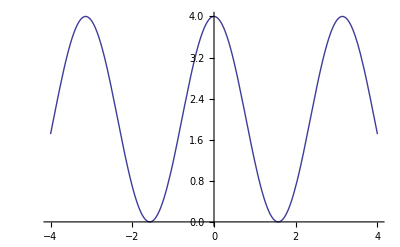

```mathematica
a=0; b= Pi/2;z=0.5; k = 1;Plot[2+2 Cos[a] Cos[2 k x],{x,-4,4}]
```

```mathematica
Clear[a,b,x,y,z,k]
```

```mathematica
ⅈ * Cross[{Exp[ⅈ k x] + Cos[a]*Exp[-ⅈ k x], Sin[a] Exp[-ⅈ k x],0},{Exp[-ⅈ k x] + Cos[a]*Exp[ⅈ k x], Sin[a] Exp[ⅈ k x],0}]//FullSimplify
```

{0,0,-2 Sin[a] Sin[2 k x]}

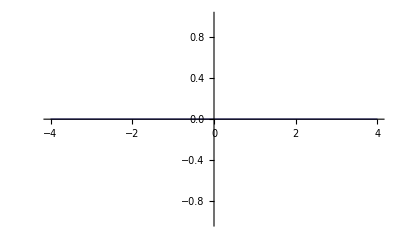

```mathematica
a=0; b= Pi/2;z=0.5; k = 1;Plot[-2 Sin[a] Sin[2 k x],{x,-4,4}]
```

```mathematica
a=1; b= Pi/2;z=0.5; k = 1;Plot3D[-2 Sin[a] Sin[2 k x],{x,-4,4},{a,-2,2}]
```

-Graphics3D-

```mathematica
x=1.6;v=0.01;ParametricPlot3D[Re[{Exp[ⅈ k v t +ⅈ t]+Cos[a] Exp[-ⅈ k  v t +ⅈ t],Sin[a] Exp[-ⅈ k v t +ⅈ t],0}],{t,0,1000}, AspectRatio->1]
```

-Graphics3D-

```mathematica
SetOptions[{Plot,ParametricPlot3D,ListPlot,ArrayPlot,ContourPlot,DiscretePlot3D},BaseStyle->{20,Directive[FontFamily->"Times New Roman"]}];
```

```mathematica
v=0.1;Show[Table[ParametricPlot3D[{0,0,x}+Re[{Exp[ⅈ k x - ⅈ t]+Cos[a] Exp[-ⅈ k  x - ⅈ t ],Sin[a] Exp[-ⅈ k x - ⅈ t ],0}],{t,0,20}, AspectRatio->1, PlotRange->{Full, Full, {0,4}}],{x,0,4,0.3}, PlotStyle-> Thick]]
```

Table::itform: Argument PlotStyle → Thick at position 3 does not have the correct form for an iterator.

Show::gtype: Table is not a type of graphics.

```mathematica
Manipulate[b= 0;z=0.5; k = 1;Show[n bTable[ParametricPlot3D[{0,0,x}+Re[{Exp[ⅈ k x-ⅈ t]+Cos[a] Exp[-ⅈ k x-ⅈ t],Sin[a] Exp[-ⅈ k x-ⅈ t],0}],{t,0,2 Pi},AspectRatio->1,PlotRange->{{-2,2},{- 2,2},{0,4}},AxesLabel -> {"x", "y", "z"},PlotStyle -> {Black,Thickness[0.003]}, Mesh -> None]/.Line[l_List]:>{{Red,Opacity[0.1],Polygon[l]},{Black,Opacity[0.3],Line[l]}} ,{x,0,4,0.3}]],{a,0, Pi}]
```

```mathematica
f[t_,u_,r_]={r (1+Cos[(8 t)]) Cos[t],r (1+Cos[8 t]) Sin[t],u};
Show[ParametricPlot3D[f[t,u,1],{t,0,2 Pi},{u,0,1},Mesh->None,PlotStyle->Opacity[.9],PlotPoints->{40,2}],ParametricPlot3D[{f[t,1,r],f[t,-1,r]},{t,0,2 Pi},{r,0,1},Mesh->None,PlotStyle->Opacity[.9],PlotPoints->{40,2}]]
```

-Graphics3D-